Write out the numerator and denominator in Lekkala2013 θ_I separately.

```mathematica
numerator = Sinh[θ1] Sinh[θ2] + α Cosh[θ1]Sinh[θ2]- λ Cosh[θ1] Cosh[θ2] + 2 λ - λ^2 Sinh[θ1]/Sinh[θ2]
```

2 λ-λ Cosh[θ1] Cosh[θ2]-λ^2 Csch[θ2] Sinh[θ1]+α Cosh[θ1] Sinh[θ2]+Sinh[θ1] Sinh[θ2]

```mathematica
denominator = Cosh[θ1] Sinh[θ2] +α Sinh[θ1]Sinh[θ2]- λ Sinh[θ1] Cosh[θ2]
```

-λ Cosh[θ2] Sinh[θ1]+Cosh[θ1] Sinh[θ2]+α Sinh[θ1] Sinh[θ2]

Divide the denominator by Cosh[θ] to see if that tames the θ1 divergence.

```mathematica
denominator/Cosh[θ1] // Simplify
```

Sinh[θ2]-λ Cosh[θ2] Tanh[θ1]+α Sinh[θ2] Tanh[θ1]

It does ...

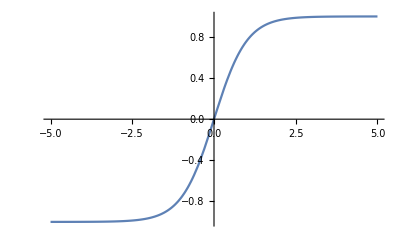

```mathematica
Plot[{Tanh[θ1]},{θ1,-5,5}]
```

... but the θ2 functions in the denominator still diverge.

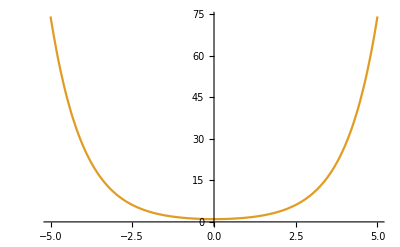

```mathematica
Plot[{Sinh[θ],Cosh[θ2]},{θ2,-5,5}]
```

Try dividing the denominator by Cosh[θ1]Cosh[θ2].

```mathematica
denominator/(Cosh[θ1]Cosh[θ2]) // Simplify
```

Tanh[θ2]+Tanh[θ1] (-λ+α Tanh[θ2])

```mathematica
Plot[Tanh[θ2],{θ2,-5,5}]
```

-Graphics-

Now, by inspection, both the θ1 and θ2 functions in the denominator are well-behaved.  What about the numerator?

```mathematica
numerator/(Cosh[θ1]Cosh[θ2]) // Simplify
```

-λ+2 λ Sech[θ1] Sech[θ2]-λ^2 Csch[θ2] Sech[θ2] Tanh[θ1]+α Tanh[θ2]+Tanh[θ1] Tanh[θ2]

All three θ2 functions in the numerator are ok at large θ2.  But one of them diverges at small θ2, which is a problem.

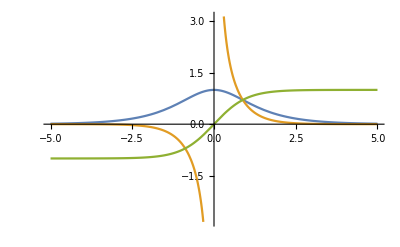

```mathematica
Plot[{Sech[θ2],Csch[θ2] Sech[θ2],Tanh[θ2]},{θ2,-5,5}]
```

This function is the culprit.

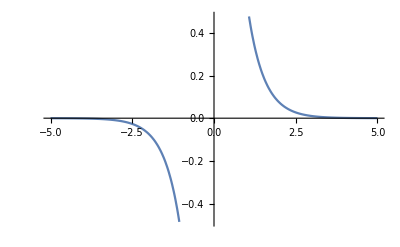

```mathematica
Plot[Csch[θ2] Sech[θ2],{θ2,-5,5}]
```

The argument θ2 = η h_s in the paper, and η does not go to zero.  So, in practice, I think the function Csch[θ2] Sech[θ2] should be ok.

In summary, write the big fraction θ_I as follows

```mathematica
(-λ+2 λ Sech[θ1] Sech[θ2]-λ^2 Csch[θ2] Sech[θ2] Tanh[θ1]+α Tanh[θ2]+Tanh[θ1] Tanh[θ2])/(Tanh[θ2]+Tanh[θ1] (-λ+α Tanh[θ2])) ;
```

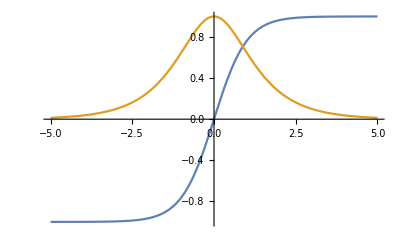

```mathematica
Plot[{Tanh[θ2],Sech[θ2]},{θ2,-5,5}]
```

Python does not have Sech and Csch function.  However, note that

```mathematica
1/Sech[θ1]
```

Cosh[θ1]

```mathematica
1/Csch[θ2]
```

Sinh[θ2]

So let us implement θ_I as (we are leaving out the ϵ_s/ϵ_eff prefactor here)

```mathematica
θI=-λ Coth[θ2]+(Tanh[θ1] Tanh[θ2]+ α Tanh[θ2]-λ+2 λ /(Cosh[θ1] Cosh[θ2])-λ^2 Tanh[θ1] /(Cosh[θ2] Sinh[θ2]))/(Tanh[θ2]+Tanh[θ1] (-λ+α Tanh[θ2])) ;
```

Check that this expression agrees with what we started with.

```mathematica
θI -( -λ Coth[θ2]+numerator/denominator) // FullSimplify
```

0

This form is well behaved because θ2 does not go to zero.  Check the large h_s limit, where θ1 and θ2 go to infinity.

```mathematica
Limit[θI,{θ1-> Infinity,θ2-> Infinity}]
```

1-λ